```mathematica
PERFrotate={};
PERFprepnd={};
```

```mathematica
(*Performance*)
PERFQUEUETEST[siz_]:=(a=ConstantArray@@{0,Round[10^(siz)]};
b=a;
aSize=Length@a;
aPtr=aSize;

aUpdate[new_]:=(a=ReplacePart[RotateRight[a,1],1->new]);

PERFrotate=Append[PERFrotate,{aSize,First@(Do[aUpdate[i],{i,1000}]//AbsoluteTiming)}];
PERFprepnd=Append[PERFprepnd,{aSize,First@(Do[b=Prepend[Drop[b,-1],i],{i,1000}]//AbsoluteTiming)}];);
(*Do[(),{siz,5,10,0.5},{num,1}]*)
PERFQUEUETEST[6]
```

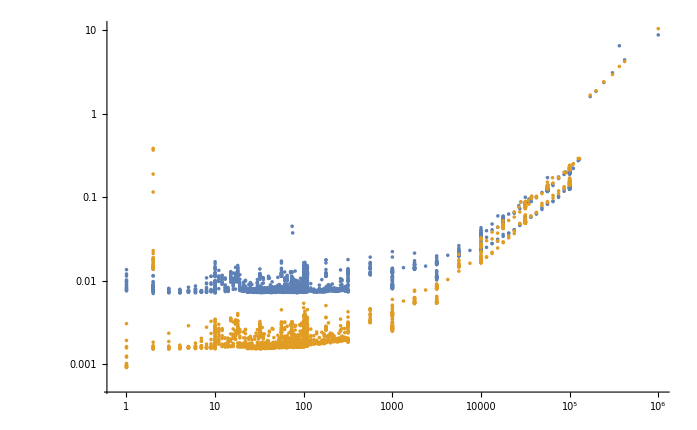

```mathematica
ListLogLogPlot[{PERFrotate,PERFprepnd},PlotRange->All]
```